## Задание 1.

Спроектируйте и создайте функции для построения выпуклой оболочки заданного множества точек плоскости с использованием алгоритма Джарвиса . Проведите тестирование .

```mathematica
ClearAll[NamedQ,𝔨𝔪];
(** Атрибуты и описание **)
𝔨𝔪::usage="Knowledge base «computer mathematics»";
SetAttributes[𝔨𝔪,{Protected,ReadProtected}];
NamedQ::usage="Check: is there a name of tested equations";
NamedQ[n1_,n2__]:=And[NamedQ[n1],NamedQ[n2]];
SetAttributes[NamedQ,Listable];
```

```mathematica
ClearAll[kmPoint];
(** Атрибуты и описание **)
SetAttributes[kmPoint,ReadProtected];
kmPoint::usage="Point on the surface";
(** Свойства **)
NamedQ[kmPoint[𝔨𝔪,id_String,___]]^:=id≠"";
kmPoint[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmPoint[𝔨𝔪,id_String,___]["id"]:=If[id=="","Point",id];
(** Конструкторы **)
kmPoint[id_String,coord:{_,_}]:=kmPoint[𝔨𝔪,id,coord];
kmPoint[coord:{_,_}]:=kmPoint[𝔨𝔪,"",coord];
kmPoint[{L1_kmLine,L2_kmLine}]:=kmPoint[#[[2]]&/@(First@NSolve@Through[{L1,L2}@"equ"])]
(** Декораторы **)
Format[P_kmPoint,StandardForm]:=Row@{P["id"],"(",Row[P["coord"],","],")"};
```

```mathematica
ClearAll[kmVector];
(** Атрибуты и описание **)
SetAttributes[kmVector,ReadProtected];
kmVector::usage="Vector on the surface";
(** Свойства **)
NamedQ[kmVector[𝔨𝔪,id_String,___]]^:=id≠"";
kmVector[𝔨𝔪,id_String,___]["id"]:=If[id=="","Vector",id];
kmVector[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmVector[𝔨𝔪,_String,coord_List,___]["norm"]:=Sqrt[Plus@@(coord*coord)];
(** Конструкторы **)
kmVector[id_String,coord_List]:=kmVector[𝔨𝔪,id,coord];
kmVector[coord_List]:=kmVector[𝔨𝔪,"",coord];
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1@"coord"-P0@"coord"];
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
MakeBoxes[V_kmVector,StandardForm]^:=TemplateBox[{V@"id",
RowBox@Riffle[MakeBoxes[#,StandardForm]&/@V["coord"],","]
},"Point2D",
DisplayFunction:>(RowBox@{OverscriptBox[#1,"⇀"],"(",#2,")"}&),
InterpretationFunction->(RowBox@{"{",#2,"}"}&),
Tooltip->Automatic];
```

```mathematica
Q=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[20]
```

{Point(,,7.65705-1.71353),Point(,,2.963849.70031),Point(,,8.178198.12093),Point(,,-9.79319-3.60396),Point(,,-5.50009-1.05228),Point(,,-3.65303-9.03034),Point(,,-6.055768.66076),Point(,,-6.39186-6.4377),Point(,,-0.4574762.93672),Point(,,-5.017013.66202),Point(,,-4.073643.04203),Point(,,9.13909-4.62079),Point(,,-0.253944-9.94279),Point(,,1.907672.83365),Point(,,7.364032.24307),Point(,,7.631021.88004),Point(,,4.042918.31276),Point(,,-9.19786-1.44139),Point(,,4.63617-0.958428),Point(,,6.71291-9.26653)}

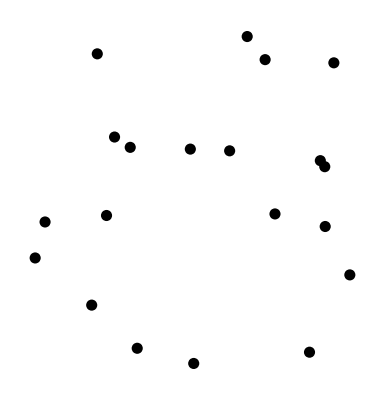

```mathematica
pointsPicture=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q}]
```

```mathematica
StartPoint=Q[[1]]
```

Point(,,7.65705-1.71353)

```mathematica
For[
i=2,i<=Length@Q,i++,
If[
And[
Or[
Q[[i]]["coord"][[2]]<StartPoint["coord"][[2]],
Q[[i]]["coord"][[2]]==StartPoint["coord"][[2]]
],
Q[[i]]["coord"][[1]]<StartPoint["coord"][[1]]
],
StartPoint=Q[[i]]
]
]
```

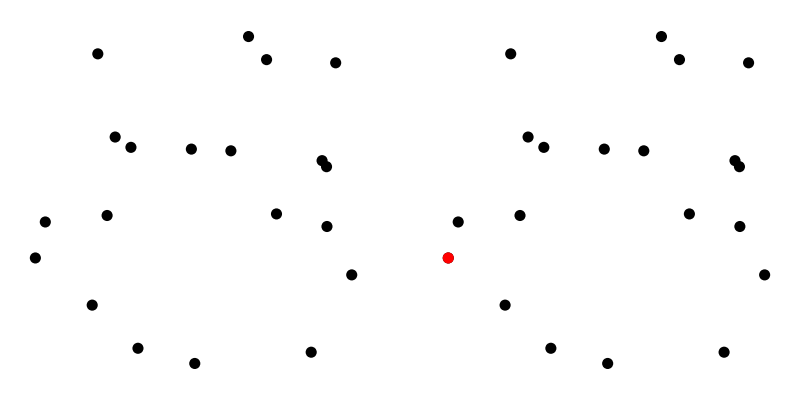

```mathematica
pointsPictureWithStartPoint=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q,Red,Point@StartPoint["coord"]}];
GraphicsRow[{pointsPicture,pointsPictureWithStartPoint},Frame->All]
```

```mathematica
L={StartPoint};
NextPoint=First@Q
CurrentPoint=Last[L]
```

Point(,,7.65705-1.71353)

Point(,,-9.79319-3.60396)

```mathematica
getTriangleAlgebraicSquare[points_List]:=Module[{a=points[[1]]["coord"],b=points[[2]]["coord"],c=points[[3]]["coord"]},1/2 Det[{b-a,c-a}]]
```

```mathematica
isPointOnLine[Line_kmLine,P_kmPoint]:=Line["equ"]/.{x->P["coord"][[1]],y->P["coord"][[2]]}
```

```mathematica
Unprotect[Unequal];
```

```mathematica
Unequal[Point1_kmPoint,Point2_kmPoint]:=Point1["coord"]!=Point2["coord"]
```

Важно закинуть стартовую точку в конец Q.

```mathematica
getStartPoint[Q_List]:=Module[{StartPoint=Q[[1]]},
For[
i=2,i<=Length@Q,i++,
If[
And[
Or[
Q[[i]]["coord"][[2]]<StartPoint["coord"][[2]],
Q[[i]]["coord"][[2]]==StartPoint["coord"][[2]]
],
Q[[i]]["coord"][[1]]<StartPoint["coord"][[1]]
],
StartPoint=Q[[i]]
]
];
Return@StartPoint
]
```

```mathematica
moveToEndOfList[lst_List,obj_]:=Append[DeleteCases[lst,obj],obj]
```

```mathematica
Q=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[50];
```

```mathematica
CH[pointsList_List]:=Module[{i=1,Q=pointsList,StartPoint,CurrentPoint,NextPoint,algebraicSquare,L={}},
StartPoint=getStartPoint[Q];
L=AppendTo[L,StartPoint];
Q=moveToEndOfList[Q,StartPoint];
CurrentPoint=StartPoint;
NextPoint=Q[[1]];
While[NextPoint!=StartPoint,
Do[
algebraicSquare=getTriangleAlgebraicSquare[{CurrentPoint,i,NextPoint}];
If[algebraicSquare>0,NextPoint=i],
{i,DeleteCases[Q,NextPoint]}
];
Q=DeleteCases[Q,NextPoint];
L=AppendTo[L,NextPoint];
If[NextPoint==StartPoint,Return@L];
CurrentPoint=NextPoint;
NextPoint=Q[[1]]
];
]
```

```mathematica
res=CH[Q]
```

{Point(,,-9.42682-9.45602),Point(,,2.73517-9.80762),Point(,,7.26092-9.72244),Point(,,9.8685-5.06952),Point(,,9.221624.97788),Point(,,8.742228.4452),Point(,,8.62369.09769),Point(,,6.721149.6392),Point(,,5.446499.51865),Point(,,-4.070498.42432),Point(,,-7.941552.9483),Point(,,-9.42682-9.45602)}

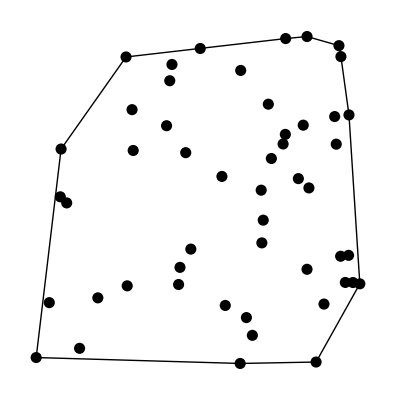

```mathematica
pointsPicture=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q,Line[{#["coord"]&/@res}]}]
```